# LU+Graph simulations of measurement of graph states

## K.S. 28 Feb 2024

## Preliminaries

### Helper functions and data structures for representing graph states and their measurement processes:

```mathematica
rules={
{before___,Subscript[P, z,sign_],Subscript[σ, z],after___}:>{before,Subscript[σ, z],Subscript[P, z,sign],after},
{before___,Subscript[P, x,sign_],Subscript[σ, z],after___}:>{before,Subscript[σ, z],Subscript[P, x,¬sign],after},
{before___,Subscript[P, y,sign_],Subscript[σ, z],after___}:>{before,Subscript[σ, z],Subscript[P, y,¬sign],after},

{before___,Subscript[P, x,sign_],√(-ⅈ Subscript[σ, z]),after___}:>{before,√(-ⅈ Subscript[σ, z]),Subscript[P, y,¬sign],after},
{before___,Subscript[P, x,sign_],√(ⅈ Subscript[σ, y]),after___}:>{before,√(ⅈ Subscript[σ, y]),Subscript[P, z,¬sign],after},
{before___,Subscript[P, x,sign_],√(-ⅈ Subscript[σ, y]),after___}:>{before,√(-ⅈ Subscript[σ, y]),Subscript[P, z,sign],after},
{before___,Subscript[P, x,sign_],√(ⅈ Subscript[σ, z]),after___}:>{before,√(ⅈ Subscript[σ, z]),Subscript[P, y,sign],after},

{before___,Subscript[P, y,sign_],√(-ⅈ Subscript[σ, z]),after___}:>{before,√(-ⅈ Subscript[σ, z]),Subscript[P, x,sign],after},
{before___,Subscript[P, y,sign_],√(ⅈ Subscript[σ, y]),after___}:>{before,√(ⅈ Subscript[σ, y]),Subscript[P, y,sign],after},
{before___,Subscript[P, y,sign_],√(-ⅈ Subscript[σ, y]),after___}:>{before,√(-ⅈ Subscript[σ, y]),Subscript[P, y,sign],after},
{before___,Subscript[P, y,sign_],√(ⅈ Subscript[σ, z]),after___}:>{before,√(ⅈ Subscript[σ, z]),Subscript[P, x,¬sign],after},

{before___,Subscript[P, z,sign_],√(-ⅈ Subscript[σ, z]),after___}:>{before,√(-ⅈ Subscript[σ, z]),Subscript[P, z,sign],after},
{before___,Subscript[P, z,sign_],√(ⅈ Subscript[σ, y]),after___}:>{before,√(ⅈ Subscript[σ, y]),Subscript[P, x,sign],after},
{before___,Subscript[P, z,sign_],√(-ⅈ Subscript[σ, y]),after___}:>{before,√(-ⅈ Subscript[σ, y]),Subscript[P, x,¬sign],after},
{before___,Subscript[P, z,sign_],√(ⅈ Subscript[σ, z]),after___}:>{before,√(ⅈ Subscript[σ, z]),Subscript[P, z,sign],after}
};
symbolrules={√x_:>MatrixPower[x,1/2],
Subscript[σ, z]->PauliMatrix[3],
Subscript[σ, y]->PauliMatrix[2],
Subscript[σ, x]->PauliMatrix[1]};
SymbolsToMatrices[ops_List]:=FullSimplify[ComplexExpand[Dot@@(ops//.symbolrules)]]
SymbolsToMatrices[{}]:=IdentityMatrix[2]
(*... and graph operations*)
Neighbors[graph_,vertex_]:=VertexList[VertexDelete[NeighborhoodGraph[graph,vertex],vertex]]

LocalGraphComplement[g_Graph,v_]:=With[{adj=AdjacencyList[g,v]},GraphUnion[GraphDifference[g,Subgraph[g,adj]],GraphComplement@Subgraph[g,adj],VertexLabels->"Name"]]
RemoveVertex[g_Graph,v_]:=VertexAdd[VertexDelete[g,v],v]

LocalComplementCommutator[graph_,vertex_,special_]:=Module[{newgraph},
newgraph=LocalGraphComplement[graph,special];
newgraph=LocalGraphComplement[newgraph,vertex];
newgraph=RemoveVertex[newgraph,vertex];
newgraph=LocalGraphComplement[newgraph,special]]

LastMost[list_]:={Last[list],Most[list]}
CommuteThrough[op_,list_]:=LastMost[({op}~Join~list)//.rules]
AppendOperations[opsold_,opsnew_]:=Module[{ops,newkeys},
newkeys=Keys[opsnew];
ops=opsold;
(ops[#]=Join[ops[#],opsnew[#]])&/@newkeys;
ops]

(* graph state operations start here. the following RawProject take a graph corresponding to a >graph state without any local unitaries<, defined only as ∏Subscript[CZ, edge]+^(⊗N) . They return an association (similar to a Python dictionary) with the next graph state and local unitaries applied to neighbour vertices, see Proposition 7 of https://arxiv.org/abs/quant-ph/0602096v1 
*)
(*True: +, False: - *)
RawProject[graph_,Subscript[P, z,sign_],vertex_]:=Module[{neighbors,newgraph,operations},
newgraph=RemoveVertex[graph,vertex];
If[sign,Return[<|"graph"->newgraph,"ops"-><||>,"probability"->1/2|>]];
neighbors=Neighbors[graph,vertex];
operations={#->{Subscript[σ, z]}}&/@neighbors;
<|"graph"->newgraph,"ops"-><|operations|>,"probability"->1/2|>
]

RawProject[graph_,Subscript[P, y,sign_],vertex_]:=Module[{neighbors,newgraph,operations,op},
newgraph=RemoveVertex[LocalGraphComplement[graph,vertex],vertex];
If[EmptyGraphQ[NeighborhoodGraph[graph,vertex]],
<|"graph"->graph,"ops"-><||>,"probability"->1/2|>];
neighbors=Neighbors[graph,vertex];

If[sign,op=√(-ⅈ Subscript[σ, z]),op=√(ⅈ Subscript[σ, z])];
operations={#->{op}}&/@neighbors;
<|"graph"->newgraph,"ops"-><|operations|>,"probability"->1/2|>
]

RawProject[graph_,Subscript[P, x,sign_],vertex_]:=Module[{neighbors,newgraph,operations,op,special,specialneighbors,tooperate,prob},

neighbors=Neighbors[graph,vertex];
If[EmptyGraphQ[NeighborhoodGraph[graph,vertex]],
(* if the vertex is disconnected, (x,-) is impossible - has probability zero. 
TODO: The code here should somehow acknowledge the above issue - send a warning/error?*)
Return@<|"graph"->graph,"ops"-><||>,"probability"->If[sign,1,0]|>
];
special=First[neighbors];
specialneighbors=Neighbors[graph,special];

newgraph=LocalComplementCommutator[graph,vertex,special];

If[sign,op=√(ⅈ Subscript[σ, y]),op=√(-ⅈ Subscript[σ, y])];
If[sign,
tooperate=Complement[neighbors,specialneighbors,{special}],
tooperate=Complement[specialneighbors,neighbors,{vertex}]];
operations={#->{Subscript[σ, z]}}&/@tooperate;
operations=Join[operations,{special->{op}}];
<|"graph"->newgraph,"ops"-><|operations|>,"probability"->1/2|>
]
(* ... but of course we're working with graph states which have been measured before, and do have some local unitaries to worry about. Similarly, 
I use table II of https://arxiv.org/abs/quant-ph/0602096v1  to commute them through and get the projector that 'acts directly on the graph state', so to say, and apply it with RawProject. The graph state gets updated, and LUs on neighboring qubits are added.
*)
Project[graphstate_Association,Subscript[P, axis_,sign_],vertex_]:=Module[{gs=graphstate,lu,newproj,ret,newgraph,newops,garbage,newprob},
lu=gs["ops"];(*local unitaries association*)
{newproj,garbage}=CommuteThrough[Subscript[P, axis,sign],lu[vertex]];

gs["measure"][vertex]=(Subscript[P, axis,sign]->newproj); (*requested projector->actually performed projector, after commuting through local ops*)

ret=RawProject[graphstate["graph"],newproj,vertex];
newgraph=ret["graph"];
newops=ret["ops"];
newprob=gs["probability"] * ret["probability"];
<|gs,"graph"->newgraph,"probability"->newprob,"ops"-><|AppendOperations[gs["ops"],newops]|>|>
]
(* also some utility functions: *)
EdgeSubgraphs[graph_Graph,nspec_]:=(*generate all edge-induced subgraph of specific number of edges*)EdgeDelete[graph,#]&/@Subsets[EdgeList[graph],nspec]
TakeOnlyConnectedPart[graph_,vertices_]:=(*restrict the graph to only the relevant part*)GraphUnion@@ConnectedGraphComponents[graph,vertices]

(* generate the graph state in the full Hilbert space: *)
FullGraphState[graph_Graph,ordering_List]:=With[{nqubits=Length@ordering,mp=PositionIndex[ordering]},
Fold[CZ[Flatten[mp/@#2],nqubits].#1& ,PlusState[nqubits],EdgeList[graph]/.UndirectedEdge->List]]/;Sort[ordering]==Sort[VertexList[graph]]

Clear[GraphSubstate]
(* generate a reduced (to qubits "terminal") state of a graph state, either defined by the graph or an Association[] describing the partially measured graph state.
NOTE: works properly only if all the non-terminal qubits have already been measured! This is a limitation induced by the FullGraphState function. *)
GraphSubstate[graph_Graph,terminal_List]:=FullGraphState[Subgraph[graph,terminal],terminal]/;SubsetQ[terminal,AdjacencyList[graph,terminal]]
GraphSubstate[gs_Association,v1_,v2_,dmatrix_:False]:=Module[{ops=SymbolsToMatrices/@gs["ops"],v},
v=KroneckerProduct[ops[v1],ops[v2]].GraphSubstate[gs["graph"],v1,v2];
v*=Sqrt[gs["probability"]];
If[dmatrix,Projector[v],v]
]/;SubsetQ[VertexList[gs["graph"]],{v1,v2}]
GraphSubstate[gs_Association,terminal_List,dmatrix_:False]:=Module[{ops=SymbolsToMatrices/@gs["ops"],v},
v=CircleTimesRedef@@(ops/@terminal).GraphSubstate[gs["graph"],terminal];
v*=Sqrt[gs["probability"]];
If[dmatrix,Projector[v],v]
]/;SubsetQ[terminal,AdjacencyList[gs["graph"],terminal]]


(*helper functions on the full Hilbert space. CircleTimes can be entered as a binary infix operator by ESCAPE c* ESCAPE*)
Clear[CircleTimes];
PlusState[nqubits_]:=1/(√(2^nqubits))ConstantArray[1,2^nqubits]
CircleTimesRedef[vec_?VectorQ]:=vec;
CircleTimesRedef[mat_?MatrixQ]:=mat;
CircleTimesRedef[vecs__]:=Flatten[KroneckerProduct@@List/@{vecs}]/;AllTrue[{vecs},VectorQ];
CircleTimesRedef[mats__]:=KroneckerProduct[mats]/;AllTrue[{mats},MatrixQ];
CircleTimes=CircleTimesRedef;
{X,Y,Z,Id}=PauliMatrix/@Range[4];
OperatorsAt[ops_Association,nqubits_]:=CircleTimesRedef@@Lookup[ops,Range[nqubits],Id]
ProjOntoOnes[indices_,nqubits_]:=OperatorsAt[<|#->DiagonalMatrix[{0,1}]&/@indices|>,nqubits]
CP[indices_,nqubits_,var_]:=MatrixExp[I var ProjOntoOnes[indices,nqubits]]
CZ[indices_,nqubits_]:=CP[indices,nqubits,π]
Projector[v_]:={v}ᵀ.{v}*
Concurrence[rho_?PositiveSemidefiniteMatrixQ,numeric_:True]:=Module[{sigma,R,sqrtrho,Y,evs},
sqrtrho=MatrixPower[rho//N,1/2];
Y=PauliMatrix[2]⊗PauliMatrix[2];
sigma=Y.Conjugate[rho//N].Y;
R=MatrixPower[sqrtrho.sigma.sqrtrho,1/2];
evs=Eigenvalues[R]//Chop;
Max[Max[evs]-(Total[evs]-Max[evs]),0]
]


(* the functions to actually use: *)

PrepareAssociation[graph_]:=Association["graph"->graph,"ops"-><|(#->{}&/@VertexList[graph])|>,"measure"-><|(#->None&/@VertexList[graph])|>,"probability"->1]
(* takes a Graph (internal Mathematica structure) and returns a fresh association corresponding to the graph state, holding the LUs and measurement outcomes. Both are initially empty. So, this association should correspond at any time to
⊗_vertex(∏_k ops[vertex][[k]])graph (first in the ops[vertex] list act last, as in matrix multiplication)
measure[qubit], if nonempty, contains a rule Subscript[P, requested axis, requested sign]->Subscript[P, actual axis, actual sign], with the actual values being different due to commuting through the local unitaries. 
 *)

ProjectAllBut[gs_Association,in_,out_,Subscript[P, axis_,sign_]]:=Fold[Project[#1,Subscript[P, axis,sign],#2]&,gs,Complement[VertexList[gs["graph"]],{in,out}]]
(*measure all qubits except (in,out) in a single outcome (e.g. Subscript[P, x,True] for (x,+)). note that it might not work properly due to the bug in RawProject*)

ProjectAllBut[gs_Association,in_,out_,projs_]:=Fold[(Project[#1,projs[#2],#2])&,gs,Complement[VertexList[gs["graph"]],{in,out}]]
(*measure all qubits except (in,out) in outcomes defined by projs association - might be taken from the output of the following function*)

ProjectAllBut[gs_Association,excl_List,projs_]:=Fold[(Project[#1,projs[#2],#2])&,gs,Complement[VertexList[gs["graph"]],excl]]
(*measure all qubits except excl=={q1,q2...} in outcomes defined by projs association - might be taken from the output of the following function*)

ProjAssociations[graph_,in_,out_,axis_]:=Module[{vs,vals,},
vs=Complement[VertexList[graph],{in,out}];
vals=Tuples[{True,False},Length[vs]];
Table[Association@MapThread[#1->Subscript[P, axis,#2]&,{vs,val}],{val,vals}]
]
ProjAssociations[graph_,excl_List,axis_]:=Module[{vs,vals,},
vs=Complement[VertexList[graph],excl];
vals=Tuples[{True,False},Length[vs]];
Table[Association@MapThread[#1->Subscript[P, axis,#2]&,{vs,val}],{val,vals}]
]
ParamProjAssociations[graph_,excl_List,axes_Association,default_]:=Module[{vs,vals,},
vs=Complement[VertexList[graph],excl];
vals=Tuples[{True,False},Length[vs]];
Table[Association@MapThread[#1->Subscript[P, Lookup[axes,#1,default],#2]&,{vs,val}],{val,vals}]
]
(*generates  way all the a priori possible measurement outcomes for measuring all qubits except (in,out) in a single axis - so all the +/True - -/False combinations, essentially. *)
```

## Exemplary calculation: fidelity of a post-measurement state when edge loss noise is present

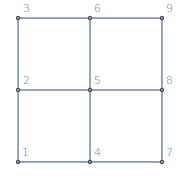

```mathematica
graph=GridGraph[{3,3},ImageSize->Small,VertexLabels->"Name"]
graphstate=PrepareAssociation[graph]; (*internal representation of the state*)
projs=ProjAssociations[graph,{1,9},x];(*list containing all of the measurement projectors associated with measuring every qubit 2..8 in x basis
(one projector for every sign structure)*);
```

```mathematica
proj=projs[[1]];(*let's pick one of the outcomes.*)
subgraphs=EdgeSubgraphs[graph,All]; (*and store the list of all edge-induced subgrapghs - this is the "uncorrelated probabilistic CZ" noise model*)
```

```mathematica
(*measure every subgraphs according to the projector "proj", and take the average over the ensemble.
Each edge is removed independently with probability p: this defines the weights (probabilities) P in the ensemble.*)
Timing[postrho=ParallelSum[Module[{gs,P,postgs,reduced},
gs=PrepareAssociation[g];
P=p^(EdgeCount[graph]-EdgeCount[g])(1-p)^EdgeCount[g];
postgs=ProjectAllBut[gs,{1,9},proj];
reduced=Evaluate@GraphSubstate[postgs,{1,9},True(*for density operator*)];
reduced*P
],{g,subgraphs}]//Expand]
```

```mathematica
(*alternatively, skip the ~3 minutes calculation and get the result:*)
postrho=;
```

```mathematica
(*The post-measurement state when no noise is present is fully entangled:*)
MatrixForm[postrho/Tr[postrho]/.p->0]
(*And completely uncorrelated if all edges are missing - without correlations, measurement does not affect the terminal qubits.*)
MatrixForm[postrho/Tr[postrho]/.p->1]
```

(1/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 0 | 0 | 1/2)

(1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4)

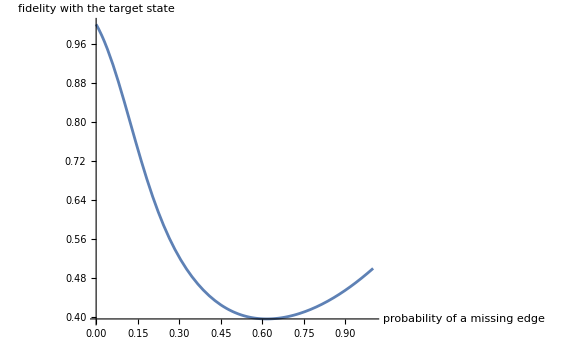

```mathematica
template=Normalize@GraphSubstate[ProjectAllBut[graphstate,{1,9},proj],{1,9}] (*the state if no noise is present (as a vector)*);
fidelity=template*.(postrho/Tr[postrho]).template//Expand//FullSimplify;
Plot[fidelity,{p,0,1},AxesLabel->{"probability of a missing edge","fidelity with the target state"},ImageSize->Large]
```